```mathematica
B[x_, degree_]:=1/(Sqrt[2 * Pi])/;degree==0
```

```mathematica
B[ x_, degree_]:= Sin[Floor[(degree + 1) / 2] * x + Mod[degree , 2] * Pi/2]/Sqrt[Pi]/;degree!=0
```

```mathematica
B@@@Table[{x, i},{i, 0, 10}]
```

{1/(√(2 π)),Cos[x]/(√π),Sin[x]/(√π),Cos[2 x]/(√π),Sin[2 x]/(√π),Cos[3 x]/(√π),Sin[3 x]/(√π),Cos[4 x]/(√π),Sin[4 x]/(√π),Cos[5 x]/(√π),Sin[5 x]/(√π)}

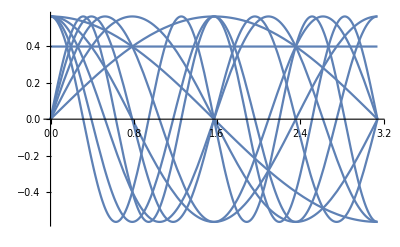

```mathematica
Plot[B@@@Table[{x, i},{i, 0, 10}], {x, 0, Pi}]
```